# f(M) from fitted GBF (WIP)

## Import data (num. GBF)

```mathematica
data1[1]={{0.004,1.152465410146683*^-10},{0.008,1.8685918018382094*^-9},{0.012,9.590120795535965*^-9},{0.016,3.073916449435129*^-8},{0.02,7.613881661556879*^-8},{0.024,1.6023705709111219*^-7},{0.028,3.013992763126808*^-7},{0.032,5.222084416798906*^-7},{0.036000000000000004,8.49906011330774*^-7},{0.04,1.3164521963762057*^-6},{0.044,1.959422135755041*^-6},{0.048,2.8224849034842437*^-6},{0.052000000000000005,3.954666037735637*^-6},{0.056,5.4130191967166935*^-6},{0.06,7.260952892260354*^-6},{0.064,9.571462116115324*^-6},{0.068,0.000012423520702678694},{0.07200000000000001,0.00001591069355136104},{0.076,0.000020128493192023944},{0.08,0.000025196860937400124},{0.084,0.000031228608078685874},{0.088,0.00003837169383276241},{0.092,0.000046770067548318394},{0.096,0.00005659319665311078},{0.1,0.0000680236124779691},{0.10400000000000001,0.00008126322904398226},{0.108,0.00009653376625318614},{0.112,0.00011407109110924549},{0.116,0.00013414702833073458},{0.12,0.0001570475303881909},{0.124,0.00018306805128649351},{0.128,0.0002125968595388513},{0.132,0.00024596571275217283},{0.136,0.00028361684801933183},{0.14,0.00032595022350970394},{0.14400000000000002,0.00037353899564481093},{0.148,0.0004267454906922144},{0.152,0.00048637142095423564},{0.156,0.0005528180239637058},{0.16,0.0006267388858254358},{0.164,0.000709090323302985},{0.168,0.0008004986795531242},{0.17200000000000001,0.000901624141572588},{0.176,0.0010138528638410464},{0.18,0.0011380745186660394},{0.184,0.0012748142661759675},{0.188,0.0014256845520091814},{0.192,0.0015920039433899688},{0.196,0.001774979075754969},{0.2,0.0019757708854302113},{0.20400000000000001,0.0021963884305447267},{0.20800000000000002,0.00243832817254291},{0.212,0.0027034028202042805},{0.216,0.0029936419047135064},{0.22,0.00331067933982809},{0.224,0.0036575443570099524},{0.228,0.004036507612075517},{0.232,0.004448776401289192},{0.23600000000000002,0.004897855914093931},{0.24,0.005391117438969532},{0.244,0.005922031509691112},{0.248,0.00650328539371402},{0.252,0.007131280329640768},{0.256,0.007818311173662839},{0.26,0.0085603568401113},{0.264,0.009366463234691928},{0.268,0.01023427282432934},{0.272,0.011185101462369118},{0.276,0.012210106786170117},{0.28,0.013318170677995256},{0.28400000000000003,0.014514474796100716},{0.28800000000000003,0.01580639126760641},{0.292,0.0171993457790485},{0.296,0.018708620632390947},{0.3,0.02033031172083099},{0.304,0.022080114621650816},{0.308,0.02395948304553439},{0.312,0.025987333657316546},{0.316,0.028171471231025595},{0.32,0.030517411805348827},{0.324,0.03302297548712414},{0.328,0.03572777989024418},{0.332,0.038604419882995185},{0.336,0.04169883205767708},{0.34,0.0449997624562594},{0.34400000000000003,0.048562146244161664},{0.34800000000000003,0.05235421313054184},{0.352,0.05639089207935622},{0.356,0.06069563186068479},{0.36,0.0652791665554143},{0.364,0.07017862624252122},{0.368,0.07541428376294443},{0.372,0.08092008162438467},{0.376,0.0868220649676948},{0.38,0.0930225152369979},{0.384,0.0996242056820896},{0.388,0.10660414078527168},{0.392,0.1139701684751544},{0.396,0.12177634669100662},{0.4,0.12993891126570478},{0.404,0.1386043456958167},{0.40800000000000003,0.14766925859721172},{0.41200000000000003,0.157119913332608},{0.41600000000000004,0.16718779753961924},{0.42,0.17766440741857015},{0.424,0.1885416962743981},{0.428,0.19992423860257236},{0.432,0.21166740674250184},{0.436,0.22402798955778533},{0.44,0.23673652786249452},{0.444,0.2500053288158481},{0.448,0.26356861270699344},{0.452,0.27767722425682806},{0.456,0.29216310164371356},{0.46,0.30721589834359825},{0.464,0.32231092418111795},{0.468,0.3379454959930605},{0.47200000000000003,0.3538100208747941},{0.47600000000000003,0.37000992009795264},{0.48,0.3864241148617551},{0.484,0.40308953175846},{0.488,0.41987135296917205},{0.492,0.436865803104247},{0.496,0.4540593424926009},{0.5,0.47106305185325603},{0.504,0.4882258275081274},{0.508,0.5054923618434738},{0.512,0.522357497333066},{0.516,0.5393504432359126},{0.52,0.5561341324082738},{0.524,0.5731841138516265},{0.528,0.5895854291677062},{0.532,0.605751181915027},{0.536,0.621800084353584},{0.54,0.6373527177866224},{0.544,0.6527156485396742},{0.548,0.6678837705215555},{0.552,0.6822965497446314},{0.556,0.6965314260174829},{0.56,0.710553529338309},{0.5640000000000001,0.7238815970862186},{0.5680000000000001,0.7370160374055996},{0.5720000000000001,0.7495396215354263},{0.5760000000000001,0.7617829887873894},{0.58,0.7735019695616826},{0.584,0.7849630119751423},{0.588,0.7955352953819556},{0.592,0.8060801543363119},{0.596,0.8160395276626904},{0.6,0.82558467284296},{0.604,0.8346972648131812},{0.608,0.8435229583101768},{0.612,0.852063640546308},{0.616,0.8598834020080076},{0.62,0.8676444308997603},{0.624,0.8749378558282938},{0.628,0.8818288689078758},{0.632,0.8885052957494926},{0.636,0.8948642828492102},{0.64,0.9005795824897266},{0.644,0.9062285535424217},{0.648,0.9114595696610391},{0.652,0.916545996813913},{0.656,0.9213139070507825},{0.66,0.9258282801789625},{0.664,0.9300580383149317},{0.668,0.9343476207604081},{0.672,0.9379681410175972},{0.676,0.9416498379212568},{0.68,0.944810508939787},{0.684,0.9481860315531213},{0.6880000000000001,0.9509449118662405},{0.6920000000000001,0.9541688548602505},{0.6960000000000001,0.9565356678547015},{0.7000000000000001,0.9592186060437163},{0.704,0.9616582414390141},{0.708,0.9637256714668425},{0.712,0.9659038282580655},{0.716,0.9678233081846256},{0.72,0.969724689813272},{0.724,0.9714943592962234},{0.728,0.9733046460326104},{0.732,0.9746644377074122},{0.736,0.976202170838451},{0.74,0.9774894159536174},{0.744,0.9789048238779833},{0.748,0.9801688850119371},{0.752,0.9812576827707168},{0.756,0.9823724671389544},{0.76,0.9833633280620103},{0.764,0.984293381511384},{0.768,0.9853931301876017},{0.772,0.98618703311257},{0.776,0.9868907677014607},{0.78,0.9878272518666832},{0.784,0.9885281420870508},{0.788,0.9890711369865278},{0.792,0.9896520511038961},{0.796,0.9902989582462789},{0.8,0.9909341454816477},{0.804,0.991431851972841},{0.808,0.991856363463604},{0.812,0.9924932256488044},{0.8160000000000001,0.9929027426893865},{0.8200000000000001,0.9933327291940971},{0.8240000000000001,0.9936966885011926},{0.8280000000000001,0.9941522951151639},{0.8320000000000001,0.994445959660592},{0.836,0.9947956243630622},{0.84,0.995085113593971},{0.844,0.9954421123695826},{0.848,0.9956517264752736},{0.852,0.995842891871443},{0.856,0.9961918117208585},{0.86,0.9964032222821942},{0.864,0.9965367345168622},{0.868,0.9967896015898388},{0.872,0.9970306394951997},{0.876,0.9971791068074238},{0.88,0.997332755179215},{0.884,0.9974653996314191},{0.888,0.9975769287679471},{0.892,0.9977892646558955},{0.896,0.9979366852448925},{0.9,0.9979860892253574},{0.904,0.9981126823171788},{0.908,0.9982211393505558},{0.912,0.9983448488995744},{0.916,0.9984298474902884},{0.92,0.998510036849335},{0.924,0.9985954005645844},{0.928,0.9986456851372173},{0.932,0.998700547219914},{0.936,0.9988214928274604},{0.9400000000000001,0.9988684744310163},{0.9440000000000001,0.9989307490852782},{0.9480000000000001,0.9989513737198527},{0.9520000000000001,0.9990540027200417},{0.9560000000000001,0.9991177793473383},{0.96,0.9991716381677784},{0.964,0.9991853262067335},{0.968,0.9992356627217788},{0.972,0.9992744671759004},{0.976,0.9993240913559612},{0.98,0.9993891032168991},{0.984,0.9994022598248058},{0.988,0.9994431164853415},{0.992,0.9994897131137409},{0.996,0.9994867737484254},{1.,0.9995140374590084},{1.004,0.9996027025899105},{1.008,0.9996103927926091},{1.012,0.9996167191608584},{1.016,0.9996301301250835},{1.02,0.99966360083266},{1.024,0.9996794937364893},{1.028,0.9996934422147552},{1.032,0.9997329825198288},{1.036,0.9997395038926082},{1.04,0.9997368073841499},{1.044,0.9997557949611799},{1.048,0.9997775928562658},{1.052,0.9997773160219743},{1.056,0.9997960278958035},{1.06,0.9998335285908245},{1.064,0.9998248482279752},{1.068,0.9998371509952161},{1.072,0.9998466099383971},{1.076,0.9998944220810073},{1.08,0.9999054953489748},{1.084,0.9998838810393714},{1.088,0.9998861795182948},{1.092,0.9998882603850994},{1.096,0.999920972241587},{1.1,0.9998915148016574},{1.104,0.999925621920158},{1.108,0.9998683619596046},{1.112,0.9999066164755861},{1.116,0.9999130932957291},{1.12,0.9999063663860329},{1.124,0.9999169143131504},{1.1280000000000001,0.9999336229493656},{1.1320000000000001,0.9999292310291904},{1.1360000000000001,0.9999130417275472},{1.1400000000000001,0.9999358890617571},{1.1440000000000001,0.9999340201140057},{1.1480000000000001,0.9999426054604081},{1.1520000000000001,0.9999503750353582},{1.156,0.9999321613429408},{1.16,0.9999463102482226},{1.164,0.9999413948680941},{1.168,0.9999427110141729},{1.172,0.9999549268355741},{1.176,0.9999532998898183},{1.18,0.9999702657077628},{1.184,0.9999522133973447},{1.188,0.9999735587575631},{1.192,0.9999518863382691},{1.196,0.9999665955852647},{1.2,0.9999718517310787},{1.204,0.9999649164083745},{1.208,0.9999817583250273},{1.212,0.9999780822741606},{1.216,0.9999764908271173},{1.22,0.9999924314238982},{1.224,0.9999798184843329},{1.228,0.999985175399726},{1.232,0.9999870372482318},{1.236,0.9999844543328475},{1.24,0.9999872268844252},{1.244,0.9999831190304959},{1.248,0.9999873752498284},{1.252,0.9999900028163009},{1.256,0.9999922072936236},{1.26,0.9999930424400361},{1.264,0.9999857389733027},{1.268,0.9999980939689804},{1.272,1.0000006060007989},{1.276,0.999990901291283},{1.28,0.9999806079353507},{1.284,0.9999934799085294},{1.288,0.9999933296502584},{1.292,0.9999936146586138},{1.296,0.999994832023071},{1.3,1.0000003781883473},{1.304,1.0000038742496957},{1.308,0.9999936737203696},{1.312,0.9999894732609718},{1.316,0.9999991230650486},{1.32,0.9999957942170506},{1.324,0.999995724835818},{1.328,0.9999903843036018},{1.332,0.9999936010630619},{1.336,0.9999918978796442},{1.34,0.9999959617426095},{1.344,0.9999961910599703},{1.348,0.9999982523538973},{1.352,0.9999954214579786},{1.356,1.000001597987952},{1.36,0.9999949268593112},{1.364,0.9999897092499295},{1.368,0.9999955350143838},{1.372,0.9999982101144875},{1.3760000000000001,1.000000977345062},{1.3800000000000001,0.9999944427354887},{1.3840000000000001,1.000002314106599},{1.3880000000000001,0.9999970173582069},{1.3920000000000001,0.9999933521411872},{1.3960000000000001,0.9999954065846246},{1.4000000000000001,0.9999967992289633},{1.4040000000000001,0.9999966913565915},{1.408,0.9999957314792678},{1.412,0.9999963728710195},{1.416,0.99999599913869},{1.42,0.9999970706691373},{1.424,1.0000002930556666},{1.428,0.9999979287287255},{1.432,0.9999995370737325},{1.436,1.0000001094568136},{1.44,0.9999996223073967},{1.444,1.000001834882901},{1.448,1.0000003341485468},{1.452,0.9999963914799469},{1.456,1.000001195804833},{1.46,1.0000030828077346},{1.464,1.000002189760552},{1.468,0.9999998711416431},{1.472,1.000000681676359},{1.476,1.000000620094632},{1.48,1.0000035567096646},{1.484,1.0000040660548324},{1.488,1.000000966180978},{1.492,1.0000013716498566},{1.496,0.9999988427429151},{1.5,1.0000000887135165},{1.504,0.9999984830181874},{1.508,0.9999991187798435},{1.512,1.000001872447655},{1.516,1.0000009737129654},{1.52,0.9999997960525818},{1.524,1.000000473937915},{1.528,0.9999999941534624},{1.532,0.9999992991747608},{1.536,0.999998237775498},{1.54,0.9999988439055151},{1.544,0.9999999697622161},{1.548,0.9999987359366755},{1.552,0.9999986572758184},{1.556,1.0000000548130512},{1.56,0.9999982161588554},{1.564,0.9999995177386599},{1.568,0.9999994785394112},{1.572,0.999999945089019},{1.576,0.9999974977002429},{1.58,0.9999999660036099},{1.584,0.9999987795027415},{1.588,0.9999981510491049},{1.592,1.0000012326981174},{1.596,0.9999995258902034},{1.6,0.999999139822283},{1.604,0.9999986930877631},{1.608,0.9999994095380444},{1.612,0.999999508290217},{1.616,0.9999996704253069},{1.62,0.9999996586717547},{1.624,0.9999987551725442},{1.6280000000000001,1.0000007071300077},{1.6320000000000001,0.9999998720642339},{1.6360000000000001,0.9999989674693294},{1.6400000000000001,0.9999994800196051},{1.6440000000000001,1.0000003726507307},{1.6480000000000001,1.000001841491321},{1.6520000000000001,1.0000006473428278},{1.6560000000000001,1.0000002206866758},{1.6600000000000001,1.0000022085490259},{1.6640000000000001,0.9999992691719279},{1.668,1.0000004417890296},{1.672,1.0000001450859497},{1.676,1.0000007657103251},{1.68,1.0000013814689175},{1.684,1.0000006946002842},{1.688,1.0000000865598828},{1.692,1.0000005419376299},{1.696,0.9999985927246615},{1.7,1.0000010327824327},{1.704,1.0000000031949643},{1.708,1.0000005082736962},{1.712,1.0000007534549096},{1.716,1.0000001146519557},{1.72,1.0000002090004554},{1.724,0.9999998659180311},{1.728,0.9999999154795618},{1.732,1.0000001654227089},{1.736,1.0000002280132678},{1.74,0.9999998510435515},{1.744,1.0000001801266474},{1.748,1.0000001354387966},{1.752,1.0000004268010925},{1.756,0.99999942387031},{1.76,0.9999998392502968},{1.764,0.9999997894198426},{1.768,0.9999995073532679},{1.772,0.9999994825612095},{1.776,0.9999995388247669},{1.78,0.9999999074364716},{1.784,1.000000000455922},{1.788,1.0000004282342216},{1.792,0.9999997046588864},{1.796,0.9999996426273574},{1.8,0.9999999492648364},{1.804,0.999999535961326},{1.808,0.9999999013373619},{1.812,0.999999795043828},{1.816,0.9999993968269655},{1.82,0.999999890478001},{1.824,0.9999998916739095},{1.828,0.9999999083482305},{1.832,0.9999998790221831},{1.836,1.0000000716632187},{1.84,0.999999834975336},{1.844,0.9999999326472989},{1.848,1.0000001056783048},{1.852,0.9999997446284087},{1.856,1.000000182555034},{1.86,1.0000001941432728},{1.864,1.000000227962264},{1.868,1.0000000346300901},{1.872,0.9999999714877286},{1.8760000000000001,0.9999999719467215},{1.8800000000000001,0.9999997480551932},{1.8840000000000001,1.0000001323611452},{1.8880000000000001,0.9999999647932947},{1.8920000000000001,1.0000000222881755},{1.8960000000000001,1.0000001521371453},{1.9000000000000001,1.0000002208570624},{1.9040000000000001,1.000000015655205},{1.9080000000000001,0.9999999549332743},{1.9120000000000001,0.9999999881760308},{1.9160000000000001,0.9999997897588961},{1.92,1.0000003123883365},{1.924,1.00000016622351},{1.928,1.0000000492174321},{1.932,1.0000003491118552},{1.936,0.9999999725605012},{1.94,1.000000025288611},{1.944,0.9999999356083925},{1.948,0.9999999157550299},{1.952,0.9999999599884322},{1.956,1.0000000525102635},{1.96,0.9999999673470781},{1.964,1.0000000723117912},{1.968,1.0000001086646066},{1.972,1.0000001026090126},{1.976,0.9999999543423815},{1.98,0.9999999141681226},{1.984,0.9999998780099819},{1.988,1.0000001474932576},{1.992,0.9999999957178052},{1.996,0.9999999992588336},{2.,1.0000000560226152},{2.004,1.000000125619289},{2.008,0.9999999031778055},{2.012,0.999999895136456},{2.016,0.9999999589928154},{2.02,0.9999999798991643},{2.024,1.0000000546585048},{2.028,0.9999999744991473},{2.032,1.0000000150157191},{2.036,0.9999999981125458},{2.04,0.9999999832614828},{2.044,1.0000000306521237},{2.048,0.9999999470126876},{2.052,1.0000000988065343},{2.056,0.9999999689746276},{2.06,1.0000000330550576},{2.064,1.0000000482511675},{2.068,1.000000017778488},{2.072,1.000000006273086},{2.076,0.9999999613606853},{2.08,1.000000054306091},{2.084,0.9999999853051631},{2.088,1.0000000420035862},{2.092,1.0000000484303333},{2.096,1.0000000418245574},{2.1,1.0000002294310775},{2.104,1.0000000701898353},{2.108,0.9999999823192902},{2.112,0.9999999056741772},{2.116,0.9999999738714355},{2.12,0.9999999874144189},{2.124,1.0000000045612165},{2.128,1.0000000066499584},{2.132,0.9999999798927808},{2.136,1.0000000510609985},{2.14,0.999999965324233},{2.144,1.000000006782046},{2.148,1.0000000079711038},{2.152,0.9999999970118731},{2.156,0.9999999932408743},{2.16,1.0000000219528797},{2.164,0.9999999955327973},{2.168,1.0000000605941781},{2.172,1.0000000301620509},{2.176,0.9999999934298912},{2.18,1.0000000226619683},{2.184,1.0000000916442404},{2.188,0.999999987993602},{2.192,1.0000000605108403},{2.196,0.9999999789020625},{2.2,1.0000000731005123},{2.204,1.0000000207199715},{2.208,0.9999999884071199},{2.212,0.9999999869513186},{2.216,1.0000000230053223},{2.22,1.0000001284251006},{2.224,1.000000007617038},{2.228,1.000000094503397},{2.232,1.0000000261523134},{2.236,0.999999998689717},{2.24,1.0000000148125292},{2.244,1.0000000113118095},{2.248,1.0000000097088633},{2.2520000000000002,0.9999999914779184},{2.2560000000000002,1.000000003244346},{2.2600000000000002,1.0000000082344929},{2.2640000000000002,1.000000052526201},{2.2680000000000002,1.0000000013441435},{2.2720000000000002,1.0000000165599408},{2.2760000000000002,0.999999997054927},{2.2800000000000002,1.000000010953088},{2.2840000000000003,1.0000000131595685},{2.2880000000000003,1.0000000103849411},{2.2920000000000003,1.000000004519091},{2.2960000000000003,1.0000000020161466},{2.3000000000000003,1.0000000083049836},{2.3040000000000003,1.0000000148141395},{2.308,1.0000000052427536},{2.312,1.000000001964155},{2.316,0.9999999941553495},{2.32,1.0000000196736694},{2.324,1.0000000111686196},{2.328,1.0000000046554605},{2.332,1.0000000287543276},{2.336,1.0000000189101412},{2.34,1.0000000293140816},{2.344,1.0000000009155756},{2.348,1.0000000023919344},{2.352,1.0000000309720933},{2.356,1.000000008289448},{2.36,1.0000000215382683},{2.364,1.0000000236196627},{2.368,1.0000000066560477},{2.372,1.0000000255394281},{2.376,1.0000000109723455},{2.38,1.00000001160786},{2.384,1.0000000015280723},{2.388,1.000000002207595},{2.392,1.0000000149502288},{2.396,0.9999999917687062},{2.4,1.000000015057311}};
data1[2]={{0.004,4.609553363692528*^-18},{0.008,2.989046776082944*^-16},{0.012,3.4507848586516757*^-15},{0.016,1.9657403772699432*^-14},{0.02,7.604970939309002*^-14},{0.024,2.3037294736303186*^-13},{0.028,5.895047825343306*^-13},{0.032,1.333349961592188*^-12},{0.036000000000000004,2.744695194361468*^-12},{0.04,5.2456136345141554*^-12},{0.044,9.441457249804845*^-12},{0.048,1.6171918549205482*^-11},{0.052000000000000005,2.657425782221843*^-11},{0.056,4.215328672090783*^-11},{0.06,6.485891731567266*^-11},{0.064,9.719203244288439*^-11},{0.068,1.423023355793842*^-10},{0.07200000000000001,2.0410413137900538*^-10},{0.076,2.874700353683957*^-10},{0.08,3.982985850901535*^-10},{0.084,5.437587528879577*^-10},{0.088,7.324939330288104*^-10},{0.092,9.74824342171557*^-10},{0.096,1.282949513930547*^-9},{0.1,1.6714744843353025*^-9},{0.10400000000000001,2.157316851751579*^-9},{0.108,2.7604630330572424*^-9},{0.112,3.504144506420897*^-9},{0.116,4.415322604906126*^-9},{0.12,5.525219419305759*^-9},{0.124,6.8696542539395844*^-9},{0.128,8.489971918575502*^-9},{0.132,1.0433955650658859*^-8},{0.136,1.2755081869346037*^-8},{0.14,1.5515537286211734*^-8},{0.14400000000000002,1.8787101725869375*^-8},{0.148,2.264750623229286*^-8},{0.152,2.718520160801241*^-8},{0.156,3.250621554522463*^-8},{0.16,3.872563564281906*^-8},{0.164,4.596850937383925*^-8},{0.168,5.4384957960282275*^-8},{0.17200000000000001,6.414814449652296*^-8},{0.176,7.540539170371441*^-8},{0.18,8.84098718919891*^-8},{0.184,1.033590710341968*^-7},{0.188,1.205305810216744*^-7},{0.192,1.401986033166418*^-7},{0.196,1.6268630466676265*^-7},{0.2,1.8832488712609758*^-7},{0.20400000000000001,2.1754517342462032*^-7},{0.20800000000000002,2.5076054292652134*^-7},{0.212,2.8846703143122534*^-7},{0.216,3.311952134599938*^-7},{0.22,3.7954674494286184*^-7},{0.224,4.3416585592132835*^-7},{0.228,4.958017703164175*^-7},{0.232,5.652289153176574*^-7},{0.23600000000000002,6.433874523912768*^-7},{0.24,7.311959087490981*^-7},{0.244,8.297189403046393*^-7},{0.248,9.400919428329342*^-7},{0.252,1.0637365330600368*^-6},{0.256,1.202322500793103*^-6},{0.26,1.356644472677235*^-6},{0.264,1.5293007049926965*^-6},{0.268,1.7216622024604989*^-6},{0.272,1.9360869028772133*^-6},{0.276,2.1744614763298284*^-6},{0.28,2.43982817489005*^-6},{0.28400000000000003,2.734208428818808*^-6},{0.28800000000000003,3.0612267885191306*^-6},{0.292,3.424225954750285*^-6},{0.296,3.826453567312299*^-6},{0.3,4.271425584015559*^-6},{0.304,4.76389912732135*^-6},{0.308,5.308728945141325*^-6},{0.312,5.910112413978669*^-6},{0.316,6.574790896171534*^-6},{0.32,7.307314767543288*^-6},{0.324,8.115624777296377*^-6},{0.328,9.006417836057044*^-6},{0.332,9.98740304563674*^-6},{0.336,0.000011066976410187279},{0.34,0.000012253625132875604},{0.34400000000000003,0.000013559545443371278},{0.34800000000000003,0.000014993928233569187},{0.352,0.000016569045762889965},{0.356,0.000018295058190887384},{0.36,0.000020193270084841906},{0.364,0.000022269228736068372},{0.368,0.000024546090718934696},{0.372,0.000027042063809560933},{0.376,0.000029770539618839766},{0.38,0.0000327567469051938},{0.384,0.00003602655050726737},{0.388,0.00003959734422872662},{0.392,0.00004350937276998236},{0.396,0.0000477690922988035},{0.4,0.00005242392626544039},{0.404,0.00005749312082509991},{0.40800000000000003,0.00006303808968334777},{0.41200000000000003,0.00006908484136513273},{0.41600000000000004,0.0000756685177990039},{0.42,0.00008285226053794232},{0.424,0.0000906668348480618},{0.428,0.00009916542903351078},{0.432,0.00010844188377115068},{0.436,0.00011851767425236687},{0.44,0.0001294834528968587},{0.444,0.00014141153245597892},{0.448,0.0001543531880468004},{0.452,0.0001684472625134818},{0.456,0.00018375510641840736},{0.46,0.00020038635700827178},{0.464,0.00021837782516130337},{0.468,0.00023799751581553053},{0.47200000000000003,0.00025920155256243415},{0.47600000000000003,0.00028229984765172693},{0.48,0.0003072872143489839},{0.484,0.0003342805736665733},{0.488,0.0003636045696886767},{0.492,0.00039550268453480714},{0.496,0.0004298783157691718},{0.5,0.0004670579008145873},{0.504,0.0005075156494093257},{0.508,0.0005512899212383228},{0.512,0.000598521191667415},{0.516,0.0006497398527956789},{0.52,0.000705067018552183},{0.524,0.0007647863815180935},{0.528,0.0008294553902633402},{0.532,0.0008993660513715436},{0.536,0.0009747798408531095},{0.54,0.0010563728469948803},{0.544,0.0011444058516222586},{0.548,0.0012394499859189007},{0.552,0.0013419981984884274},{0.556,0.001452608602331825},{0.56,0.0015719257845525898},{0.5640000000000001,0.001700918856292572},{0.5680000000000001,0.0018401304694499667},{0.5720000000000001,0.001989768795082422},{0.5760000000000001,0.0021518759266547023},{0.58,0.00232594442771676},{0.584,0.002513662150008354},{0.588,0.0027148831275362263},{0.592,0.002933246840474167},{0.596,0.003167306238454324},{0.6,0.0034201776763866398},{0.604,0.0036917277030855335},{0.608,0.00398374504755913},{0.612,0.00429733831073767},{0.616,0.004635969385874973},{0.62,0.004999225341760689},{0.624,0.005390877505165425},{0.628,0.005811502383948809},{0.632,0.006263438430610894},{0.636,0.006748296143347313},{0.64,0.007271055400385891},{0.644,0.00783117173087239},{0.648,0.00843350669740648},{0.652,0.009075720574630157},{0.656,0.00976779807741582},{0.66,0.0105145643686529},{0.664,0.01130851943553709},{0.668,0.012168364551345987},{0.672,0.013081256331767885},{0.676,0.014066520811754427},{0.68,0.015119458871726095},{0.684,0.01625530962761758},{0.6880000000000001,0.017460319742402666},{0.6920000000000001,0.01875335151960504},{0.6960000000000001,0.020134336605069813},{0.7000000000000001,0.021620054866968937},{0.704,0.02320194297736888},{0.708,0.02489371528771315},{0.712,0.026709838214150038},{0.716,0.02864289550131911},{0.72,0.03071539300470891},{0.724,0.032922567003058255},{0.728,0.03527748123346766},{0.732,0.03778998974043193},{0.736,0.040460923289620344},{0.74,0.0433325321987529},{0.744,0.046349555617694695},{0.748,0.049586528769745515},{0.752,0.05302457403600252},{0.756,0.056665540478618874},{0.76,0.06056862877317249},{0.764,0.06469323063023014},{0.768,0.06910086358963345},{0.772,0.0737237472795844},{0.776,0.07868857920634444},{0.78,0.08386738158070746},{0.784,0.08935933091859212},{0.788,0.09523759860700669},{0.792,0.10136997181120581},{0.796,0.10784785356607723},{0.8,0.11468604700201095},{0.804,0.12191934947538689},{0.808,0.12948574218111317},{0.812,0.1374718902181781},{0.8160000000000001,0.1458323382476726},{0.8200000000000001,0.15457703553584662},{0.8240000000000001,0.1637422107940265},{0.8280000000000001,0.17339885008954883},{0.8320000000000001,0.18339838931055105},{0.836,0.1938160119874946},{0.84,0.204726466845431},{0.844,0.21600229745590632},{0.848,0.2277870199793833},{0.852,0.23992077893347055},{0.856,0.25241025093654956},{0.86,0.2654851422712565},{0.864,0.2786958983857054},{0.868,0.29264822176495103},{0.872,0.3066892018216145},{0.876,0.32130381325934576},{0.88,0.3360940275924573},{0.884,0.35121063916234907},{0.888,0.3667097956316551},{0.892,0.38251650889714695},{0.896,0.39840508826999715},{0.9,0.4144786605423967},{0.904,0.43094192146412036},{0.908,0.4472959013873707},{0.912,0.463789485535253},{0.916,0.48034905382866144},{0.92,0.4968779830538498},{0.924,0.5134522915285958},{0.928,0.5300335941282212},{0.932,0.5463685421620056},{0.936,0.5626750368610293},{0.9400000000000001,0.5787924251901087},{0.9440000000000001,0.5949091849459176},{0.9480000000000001,0.6106736560042969},{0.9520000000000001,0.6261364419624421},{0.9560000000000001,0.6413232870162782},{0.96,0.6563647707207723},{0.964,0.6709885419928113},{0.968,0.6849171979573704},{0.972,0.6989376901080651},{0.976,0.712676759889479},{0.98,0.7256596312709435},{0.984,0.7383669380732208},{0.988,0.7507798806334117},{0.992,0.7627550551600043},{0.996,0.7745413820339203},{1.,0.7854638940686663},{1.004,0.796138297176004},{1.008,0.8063147025639948},{1.012,0.8166951461823789},{1.016,0.8258414983255302},{1.02,0.8348248562177737},{1.024,0.8435319844517655},{1.028,0.8520830055562794},{1.032,0.8596822407807384},{1.036,0.8672340405012273},{1.04,0.8745581618243607},{1.044,0.8812032981593394},{1.048,0.8879879075836296},{1.052,0.8942972279620288},{1.056,0.9001260730714865},{1.06,0.9057997077327178},{1.064,0.9110338998759616},{1.068,0.9160672651036558},{1.072,0.9208693171014857},{1.076,0.9253992783881239},{1.08,0.9296618556560516},{1.084,0.9337370876196371},{1.088,0.9374189191618879},{1.092,0.9412243511990769},{1.096,0.9447597401506826},{1.1,0.9477568048382837},{1.104,0.9508669276937591},{1.108,0.9537450236639125},{1.112,0.9566414105015656},{1.116,0.9590929729408185},{1.12,0.961413632209365},{1.124,0.9637229135280057},{1.1280000000000001,0.9657373372086419},{1.1320000000000001,0.9676975564049922},{1.1360000000000001,0.969733758858045},{1.1400000000000001,0.9715579744846525},{1.1440000000000001,0.9731824712095887},{1.1480000000000001,0.974753553840735},{1.1520000000000001,0.9761829132207809},{1.156,0.9775864035599136},{1.16,0.9788772481639288},{1.164,0.9801882736449772},{1.168,0.9813906518313669},{1.172,0.9824710705434991},{1.176,0.9835106804309677},{1.18,0.9844842211437054},{1.184,0.9854370305549822},{1.188,0.9862804193932864},{1.192,0.9871316035555218},{1.196,0.9878366682234925},{1.2,0.9885062288566323},{1.204,0.9892304263673847},{1.208,0.9899202372687889},{1.212,0.990432776631181},{1.216,0.991028258590036},{1.22,0.9916437171361283},{1.224,0.9920630364704078},{1.228,0.992544523105252},{1.232,0.9930040780075349},{1.236,0.9934289199247206},{1.24,0.9937812365763506},{1.244,0.994203207544286},{1.248,0.9945125669210967},{1.252,0.994879100583947},{1.256,0.9951561149122513},{1.26,0.9954591403760698},{1.264,0.9957073480325687},{1.268,0.9959802339349062},{1.272,0.9962666151067564},{1.276,0.99646684866734},{1.28,0.996634624564421},{1.284,0.996828203778471},{1.288,0.9970366963120821},{1.292,0.9972164630944068},{1.296,0.9973761844639475},{1.3,0.9975470520349138},{1.304,0.9977436069204147},{1.308,0.9978303931920712},{1.312,0.9979209995497929},{1.316,0.9980733115507056},{1.32,0.9981937952708778},{1.324,0.9983200557437726},{1.328,0.9983803351424811},{1.332,0.9984781576569497},{1.336,0.9985635331722954},{1.34,0.9986241751259732},{1.344,0.9987532466559795},{1.348,0.9988133050218815},{1.352,0.9988766229152466},{1.356,0.9989276957329288},{1.36,0.9989863332918488},{1.364,0.9990514996576826},{1.368,0.9990877211123181},{1.372,0.9991793622229117},{1.3760000000000001,0.9992133455060936},{1.3800000000000001,0.9992329408417817},{1.3840000000000001,0.9992880141305599},{1.3880000000000001,0.9993140667308369},{1.3920000000000001,0.9993435984058395},{1.3960000000000001,0.9993707209383633},{1.4000000000000001,0.9994528269932055},{1.4040000000000001,0.9994192204635733},{1.408,0.999507082514247},{1.412,0.9995433600516849},{1.416,0.9995794552674145},{1.42,0.9995991529161841},{1.424,0.9996246648415018},{1.428,0.9996180627665942},{1.432,0.9996630182495224},{1.436,0.9996786632502211},{1.44,0.9997114782683656},{1.444,0.9997244356686512},{1.448,0.9997493863588204},{1.452,0.999752747820375},{1.456,0.9997609020752366},{1.46,0.9997975297995298},{1.464,0.9997831878808254},{1.468,0.999813517513455},{1.472,0.9998073122576723},{1.476,0.9998421462292864},{1.48,0.9998452190644931},{1.484,0.9998628321864078},{1.488,0.9998615296597996},{1.492,0.9998784843203612},{1.496,0.999875215770271},{1.5,0.9998855305260765},{1.504,0.9999055118531294},{1.508,0.9998899904171124},{1.512,0.9998927157181648},{1.516,0.9999187627345342},{1.52,0.9998934306580444},{1.524,0.999924892488497},{1.528,0.9999259242369272},{1.532,0.999924797350751},{1.536,0.9999088415682464},{1.54,0.9999320371366085},{1.544,0.9999327855061394},{1.548,0.9999330321471358},{1.552,0.9999472222197092},{1.556,0.999942345125908},{1.56,0.9999380111478913},{1.564,0.9999560399185875},{1.568,0.999952966917271},{1.572,0.9999521200731697},{1.576,0.9999537457248953},{1.58,0.9999593559596507},{1.584,0.9999580031522146},{1.588,0.9999636017112131},{1.592,0.9999611623853044},{1.596,0.9999608504505291},{1.6,0.9999706461932213},{1.604,0.9999716574289359},{1.608,0.9999731864277778},{1.612,0.9999716797351066},{1.616,0.9999755109189092},{1.62,0.9999745276572547},{1.624,0.9999768699370007},{1.6280000000000001,0.9999691037030849},{1.6320000000000001,0.9999872129807522},{1.6360000000000001,0.9999783856167714},{1.6400000000000001,0.9999916307459068},{1.6440000000000001,0.9999844477905078},{1.6480000000000001,0.9999844833471296},{1.6520000000000001,0.9999843509932598},{1.6560000000000001,0.9999891087912771},{1.6600000000000001,0.9999868867868416},{1.6640000000000001,0.9999880736385297},{1.668,0.9999945557701393},{1.672,0.9999927663652365},{1.676,0.9999950305715035},{1.68,0.9999951086554765},{1.684,0.9999949083031487},{1.688,0.9999920907473061},{1.692,0.999993935510177},{1.696,0.9999909855542937},{1.7,0.9999945663498406},{1.704,0.9999936434689756},{1.708,1.0000119266574259},{1.712,0.9999980107653489},{1.716,0.9999953564261607},{1.72,0.9999973127327202},{1.724,0.9999956861127951},{1.728,0.9999952408520322},{1.732,0.9999965882287877},{1.736,0.9999949697867959},{1.74,0.9999964299086921},{1.744,0.9999954254552579},{1.748,0.9999973885756653},{1.752,0.9999951055803546},{1.756,0.9999947191827406},{1.76,0.9999965244595432},{1.764,0.9999979337769109},{1.768,0.9999977456493891},{1.772,0.999996745184167},{1.776,0.9999958857279705},{1.78,0.9999992826412525},{1.784,0.9999982580176543},{1.788,0.9999951374883786},{1.792,0.999999259640118},{1.796,0.9999982343363863},{1.8,0.9999987991525869},{1.804,0.9999986840636467},{1.808,0.9999990588179374},{1.812,0.9999974123550095},{1.816,1.0000051796641456},{1.82,0.9999981105055996},{1.824,0.9999988903259337},{1.828,1.0000016890947345},{1.832,0.9999972738213119},{1.836,0.9999989342428822},{1.84,0.9999998163685813},{1.844,0.9999983692525752},{1.848,0.9999987472605625},{1.852,0.9999993178546637},{1.856,0.9999997489131245},{1.86,1.0000003872551768},{1.864,0.999999723027963},{1.868,0.99999901179796},{1.872,1.000000434222743},{1.8760000000000001,0.999998815069388},{1.8800000000000001,0.9999999535218046},{1.8840000000000001,0.9999991058246873},{1.8880000000000001,1.000000323082519},{1.8920000000000001,0.9999994430231948},{1.8960000000000001,1.0000016275614791},{1.9000000000000001,1.0000008329496137},{1.9040000000000001,0.9999998032003893},{1.9080000000000001,0.9999991661271604},{1.9120000000000001,1.0000005270449297},{1.9160000000000001,1.0000011761405305},{1.92,1.0000004900576345},{1.924,0.9999996814093634},{1.928,1.0000003914886073},{1.932,0.9999988908832895},{1.936,0.9999999529305412},{1.94,1.0000013739862954},{1.944,0.9999993691216339},{1.948,0.9999991362948694},{1.952,0.9999992091588877},{1.956,0.999999160312372},{1.96,0.9999993231915725},{1.964,0.999999591426131},{1.968,1.0000001182833338},{1.972,0.9999992113773701},{1.976,0.9999998093398198},{1.98,0.9999991010162813},{1.984,0.9999992107614851},{1.988,0.9999998278419971},{1.992,0.9999993193376547},{1.996,0.9999988121751111},{2.,0.9999994659221486},{2.004,1.0000001711691284},{2.008,0.9999999403259996},{2.012,0.9999999475683113},{2.016,1.0000000087725713},{2.02,0.9999998334181353},{2.024,0.9999999863707227},{2.028,1.000000354856855},{2.032,1.0000005675079384},{2.036,0.9999997636426158},{2.04,1.0000008567464016},{2.044,1.0000001634015452},{2.048,0.9999999109342897},{2.052,0.9999999472035058},{2.056,0.9999996950718708},{2.06,1.0000000777382996},{2.064,1.000000089651431},{2.068,1.0000005219894714},{2.072,1.0000005060979555},{2.076,1.0000000417571482},{2.08,1.0000000001118015},{2.084,1.0000002114564026},{2.088,1.0000006104256216},{2.092,0.9999995867550271},{2.096,1.0000002290424133},{2.1,1.000000334675192},{2.104,0.9999999523807201},{2.108,1.0000001643869147},{2.112,1.0000001913162813},{2.116,1.0000002329793352},{2.12,1.000000311021132},{2.124,0.999999996226853},{2.128,0.9999999483822424},{2.132,1.0000002440127063},{2.136,1.0000000195786374},{2.14,1.0000000154136413},{2.144,0.9999997703565114},{2.148,0.9999998759310798},{2.152,1.0000000442878936},{2.156,1.0000001262790197},{2.16,1.000000105605055},{2.164,0.999999892264037},{2.168,1.0000001026463923},{2.172,0.9999999595679493},{2.176,1.0000001991130498},{2.18,1.0000000335966248},{2.184,1.0000000852230881},{2.188,1.0000001396950098},{2.192,1.000000090975808},{2.196,1.000000011354452},{2.2,1.0000001980787283},{2.204,0.9999998635129334},{2.208,1.0000001605793556},{2.212,1.0000000039547474},{2.216,1.0000001170728716},{2.22,0.999999937317685},{2.224,0.9999996660590269},{2.228,0.9999998195682657},{2.232,1.0000000304064232},{2.236,1.000000000065307},{2.24,1.0000001655295614},{2.244,0.9999999744800747},{2.248,1.0000000402781086},{2.2520000000000002,0.9999999937512603},{2.2560000000000002,0.9999999101317064},{2.2600000000000002,0.9999999987981616},{2.2640000000000002,1.0000000382914496},{2.2680000000000002,1.0000000138236262},{2.2720000000000002,1.0000001357772739},{2.2760000000000002,1.0000001167145611},{2.2800000000000002,1.00000012885113},{2.2840000000000003,1.0000000757283427},{2.2880000000000003,0.9999999685710155},{2.2920000000000003,1.0000000681753833},{2.2960000000000003,1.00000010600998},{2.3000000000000003,1.0000000789658523},{2.3040000000000003,0.9999998611251235},{2.308,1.00000001987961},{2.312,1.0000000489158325},{2.316,0.9999999899429538},{2.32,0.9999999569110504},{2.324,1.0000000395319582},{2.328,1.0000000336789114},{2.332,1.0000000396584245},{2.336,0.9999999759785634},{2.34,1.0000000862432126},{2.344,1.0000000260040731},{2.348,1.0000000193487595},{2.352,0.9999999991578293},{2.356,1.0000000636331887},{2.36,1.0000000192454859},{2.364,0.9999999326076762},{2.368,1.0000000845024395},{2.372,1.000000062852874},{2.376,0.9999999406858782},{2.38,0.9999998954326754},{2.384,1.000000084065198},{2.388,1.0000000194429979},{2.392,0.9999999138854649},{2.396,1.000000053481542},{2.4,1.000000034077506}};

data1[3]={{0.004,2.7759861895307815*^-24},{0.008,2.7759861895307815*^-23},{0.012,7.210162595653937*^-22},{0.016,7.30095595750034*^-21},{0.02,4.412741037757617*^-20},{0.024,1.924558057049758*^-19},{0.028,6.701926319946156*^-19},{0.032,1.979451547952725*^-18},{0.036000000000000004,5.155876134793439*^-18},{0.04,1.216210922744878*^-17},{0.044,2.64799841820665*^-17},{0.048,5.396442030320344*^-17},{0.052000000000000005,1.040402326787843*^-16},{0.056,1.9133537480839125*^-16},{0.06,3.3784930360375607*^-16},{0.064,5.758218707998713*^-16},{0.068,9.514060467016398*^-16},{0.07200000000000001,1.5293805359971917*^-15},{0.076,2.398990835247845*^-15},{0.08,3.681425562486218*^-15},{0.084,5.538826232547902*^-15},{0.088,8.185334093819702*^-15},{0.092,1.1900853985853253*^-14},{0.096,1.7046974842014955*^-14},{0.1,2.4087216221229087*^-14},{0.10400000000000001,3.360979178237482*^-14},{0.108,4.635588100740541*^-14},{0.112,6.325289453741516*^-14},{0.116,8.545161386501028*^-14},{0.12,1.1437414125372316*^-13},{0.124,1.5176612774608742*^-13},{0.128,1.9975664931788155*^-13},{0.132,2.609349274075875*^-13},{0.136,3.3842793181539195*^-13},{0.14,4.3600637397912554*^-13},{0.14400000000000002,5.581917278484688*^-13},{0.148,7.103523238006986*^-13},{0.152,8.988960747049632*^-13},{0.156,1.131541219559077*^-12},{0.16,1.4171768658037657*^-12},{0.164,1.766332958725154*^-12},{0.168,2.1916592336191092*^-12},{0.17200000000000001,2.7074883366434105*^-12},{0.176,3.3311029387067865*^-12},{0.18,4.082380849061705*^-12},{0.184,4.983939922303739*^-12},{0.188,6.063232956087264*^-12},{0.192,7.351139026698917*^-12},{0.196,8.882716968671276*^-12},{0.2,1.0700811190830188*^-11},{0.20400000000000001,1.2851681110950458*^-11},{0.20800000000000002,1.5389919862023644*^-11},{0.212,1.8378799986155217*^-11},{0.216,2.1889710591268904*^-11},{0.22,2.600438749064872*^-11},{0.224,3.081828472636955*^-11},{0.228,3.643488464552141*^-11},{0.232,4.2977022629148956*^-11},{0.23600000000000002,5.058247727912176*^-11},{0.24,5.94074168899989*^-11},{0.244,6.962666527160733*^-11},{0.248,8.144745659884365*^-11},{0.252,9.509059791484229*^-11},{0.256,1.1080977679428937*^-10},{0.26,1.2891112368120345*^-10},{0.264,1.496836004818077*^-10},{0.268,1.735335493305759*^-10},{0.272,2.0084934161657576*^-10},{0.276,2.3210080105736497*^-10},{0.28,2.6780336672082156*^-10},{0.28400000000000003,3.085465259994174*^-10},{0.28800000000000003,3.5498758566057183*^-10},{0.292,4.0782913795545905*^-10},{0.296,4.678831989050312*^-10},{0.3,5.361024494312419*^-10},{0.304,6.134718624116002*^-10},{0.308,7.011702415400588*^-10},{0.312,8.004152355649948*^-10},{0.316,9.125823906293129*^-10},{0.32,1.0393865661733825*^-9},{0.324,1.1824832141536075*^-9},{0.328,1.3437104593063053*^-9},{0.332,1.5253752752358899*^-9},{0.336,1.7297969696473912*^-9},{0.34,1.9595821754194114*^-9},{0.34400000000000003,2.217830452681326*^-9},{0.34800000000000003,2.5076885904172148*^-9},{0.352,2.832709279839108*^-9},{0.356,3.196981553462722*^-9},{0.36,3.6049513377005465*^-9},{0.364,4.061348686105762*^-9},{0.368,4.571597784291734*^-9},{0.372,5.1418041709493005*^-9},{0.376,5.778795075297357*^-9},{0.38,6.488816879512608*^-9},{0.384,7.2812732036538*^-9},{0.388,8.163798700072999*^-9},{0.392,9.146359551030678*^-9},{0.396,1.0239479476961264*^-8},{0.4,1.1454841236052655*^-8},{0.404,1.2807495425770279*^-8},{0.40800000000000003,1.4308594710958217*^-8},{0.41200000000000003,1.5974914730864772*^-8},{0.41600000000000004,1.7824675645491213*^-8},{0.42,1.987481152873303*^-8},{0.424,2.21466039536224*^-8},{0.428,2.466518331068892*^-8},{0.432,2.7454196026379652*^-8},{0.436,3.053482446480956*^-8},{0.44,3.39471811985373*^-8},{0.444,3.771481121953995*^-8},{0.448,4.188135805712426*^-8},{0.452,4.64787728150845*^-8},{0.456,5.155746485683868*^-8},{0.46,5.715900398244897*^-8},{0.464,6.333596581766511*^-8},{0.468,7.014736041475391*^-8},{0.47200000000000003,7.764813783839329*^-8},{0.47600000000000003,8.591144025970807*^-8},{0.48,9.501139174489434*^-8},{0.484,1.0502711101119724*^-7},{0.488,1.1602679775700806*^-7},{0.492,1.2813619133341963*^-7},{0.496,1.4145297619352623*^-7},{0.5,1.5606439978622732*^-7},{0.504,1.7213421578857662*^-7},{0.508,1.897576153954572*^-7},{0.512,2.0909277588551692*^-7},{0.516,2.302925394296597*^-7},{0.52,2.5361717455998543*^-7},{0.524,2.791008629625783*^-7},{0.528,3.070956798790484*^-7},{0.532,3.3772777903153105*^-7},{0.536,3.712602772443318*^-7},{0.54,4.07996733117334*^-7},{0.544,4.4818065369749094*^-7},{0.548,4.921886142532258*^-7},{0.552,5.40304159723309*^-7},{0.556,5.928744657774246*^-7},{0.56,6.503673966142823*^-7},{0.5640000000000001,7.132056249988129*^-7},{0.5680000000000001,7.817915593803715*^-7},{0.5720000000000001,8.567772437412271*^-7},{0.5760000000000001,9.386301537493521*^-7},{0.58,1.0278599306401306*^-6},{0.584,1.1253572587491632*^-6},{0.588,1.2316764858104474*^-6},{0.592,1.3476756617547173*^-6},{0.596,1.4739399131880439*^-6},{0.6,1.6117573562109155*^-6},{0.604,1.7619632392763549*^-6},{0.608,1.9254968479715647*^-6},{0.612,2.103324630474207*^-6},{0.616,2.2969073230252475*^-6},{0.62,2.5082578513254316*^-6},{0.624,2.738064056974032*^-6},{0.628,2.9880211573429713*^-6},{0.632,3.259367164567126*^-6},{0.636,3.5550194487036105*^-6},{0.64,3.876704258704645*^-6},{0.644,4.226425859992149*^-6},{0.648,4.605632986312763*^-6},{0.652,5.018229486536499*^-6},{0.656,5.466218864183534*^-6},{0.66,5.953274322352026*^-6},{0.664,6.4815352735281336*^-6},{0.668,7.05483186248619*^-6},{0.672,7.678366000260364*^-6},{0.676,8.352349926149752*^-6},{0.68,9.086706533913661*^-6},{0.684,9.880969902940833*^-6},{0.6880000000000001,0.00001074295697161605},{0.6920000000000001,0.000011678634894853243},{0.6960000000000001,0.000012691584302938827},{0.7000000000000001,0.000013788077941880706},{0.704,0.000014980476753242388},{0.708,0.000016271328581999046},{0.712,0.00001766726983353538},{0.716,0.000019178410390965716},{0.72,0.000020810886449039297},{0.724,0.000022581333530263137},{0.728,0.0000245107891065488},{0.732,0.00002658878597075451},{0.736,0.00002883303752702114},{0.74,0.000031262730673602494},{0.744,0.00003389870494207412},{0.748,0.000036744157035999424},{0.752,0.00003981700400179922},{0.756,0.00004314119965113219},{0.76,0.00004674257572298627},{0.764,0.00005061932490002791},{0.768,0.000054825020952940085},{0.772,0.00005936395743485738},{0.776,0.0000642610041659715},{0.78,0.000069545943460031},{0.784,0.00007527637263860571},{0.788,0.00008144849692982155},{0.792,0.00008813448426441486},{0.796,0.00009530159114990163},{0.8,0.00010306077991025322},{0.804,0.0001114491339304178},{0.808,0.00012045871645364475},{0.812,0.0001302397366390052},{0.8160000000000001,0.00014076405112365052},{0.8200000000000001,0.00015205798093734859},{0.8240000000000001,0.00016430974118553782},{0.8280000000000001,0.00017750822119746222},{0.8320000000000001,0.0001917211524830296},{0.836,0.00020703186553879002},{0.84,0.00022356971187074954},{0.844,0.00024134874283796365},{0.848,0.0002605629804792373},{0.852,0.0002811551975582698},{0.856,0.00030337440434169145},{0.86,0.00032735339168382243},{0.864,0.0003531338208654973},{0.868,0.00038093421421869577},{0.872,0.0004108469973388378},{0.876,0.00044308685733206117},{0.88,0.00047778909264055186},{0.884,0.0005150908554267177},{0.888,0.0005550622659586157},{0.892,0.0005983699854579422},{0.896,0.0006447775996653494},{0.9,0.0006948638018382602},{0.904,0.000748568134473007},{0.908,0.0008060300124319656},{0.912,0.0008687169034961114},{0.916,0.0009355398606955072},{0.92,0.0010072530777767187},{0.924,0.0010844379362681407},{0.928,0.0011678981944738803},{0.932,0.0012565205646079124},{0.936,0.0013531924196630465},{0.9400000000000001,0.0014556203970762496},{0.9440000000000001,0.0015663825488276073},{0.9480000000000001,0.0016850703954052566},{0.9520000000000001,0.0018127959125995249},{0.9560000000000001,0.0019504075849016858},{0.96,0.0020970635624890065},{0.964,0.0022556413309807524},{0.968,0.0024256311533084264},{0.972,0.002607187796090693},{0.976,0.002803341545960645},{0.98,0.0030126221415637876},{0.984,0.00323768848328349},{0.988,0.0034789838596976565},{0.992,0.0037386419844475166},{0.996,0.0040160402803582065},{1.,0.004314174636755405},{1.004,0.004632283524964662},{1.008,0.0049792949565444005},{1.012,0.005344239370552771},{1.016,0.005737246897170449},{1.02,0.0061580726455510906},{1.024,0.006611785730043295},{1.028,0.007095295225115796},{1.032,0.007614123745163028},{1.036,0.008169798027089172},{1.04,0.00876558706906024},{1.044,0.009399840258791174},{1.048,0.010083556806527106},{1.052,0.01081149731383576},{1.056,0.011589475791883961},{1.06,0.012428189914572021},{1.064,0.013321854790193335},{1.068,0.014278341604844877},{1.072,0.015296589810324128},{1.076,0.01638814071758554},{1.08,0.017549988713770826},{1.084,0.018805922908529196},{1.088,0.020133001351578913},{1.092,0.02154884605576714},{1.096,0.023068927833032424},{1.1,0.024693314210630188},{1.104,0.026438001241966304},{1.108,0.028265514817603418},{1.112,0.030245640015105775},{1.116,0.03234522529169698},{1.12,0.034577898261005956},{1.124,0.03697230194694979},{1.1280000000000001,0.039500904485951394},{1.1320000000000001,0.04220512218762545},{1.1360000000000001,0.045066046748337175},{1.1400000000000001,0.048125141876433394},{1.1440000000000001,0.051374675697764036},{1.1480000000000001,0.05480293422700044},{1.1520000000000001,0.05847997728021305},{1.156,0.062372444286979994},{1.16,0.06651056858916438},{1.164,0.07086264694001819},{1.168,0.07548875867294465},{1.172,0.08039166457426539},{1.176,0.08557452718002306},{1.18,0.09107868120931634},{1.184,0.09680271821005207},{1.188,0.10294925872484541},{1.192,0.10935306085960847},{1.196,0.11612862822663653},{1.2,0.12325280658419442},{1.204,0.13070954258306636},{1.208,0.13866843916555008},{1.212,0.14688548968645931},{1.216,0.1554984075549723},{1.22,0.16459492743869394},{1.224,0.17398149971442484},{1.228,0.18388004963487026},{1.232,0.19415893823276895},{1.236,0.20486163641494265},{1.24,0.2159527547356539},{1.244,0.22754882000839308},{1.248,0.23946296769715295},{1.252,0.25179184771444013},{1.256,0.2646769441293996},{1.26,0.2777622790427585},{1.264,0.2913043967228293},{1.268,0.3051672230231941},{1.272,0.3195065024141616},{1.276,0.33418581745475734},{1.28,0.349215887337848},{1.284,0.3645176486144243},{1.288,0.3797976744751787},{1.292,0.3957410938440243},{1.296,0.41134448653554856},{1.3,0.42753826864986516},{1.304,0.44381876252485436},{1.308,0.46016983109145077},{1.312,0.4764411315637538},{1.316,0.49308610200141145},{1.32,0.5095442757742951},{1.324,0.5259205574207576},{1.328,0.5422359429410546},{1.332,0.5584452367562565},{1.336,0.5745135391263637},{1.34,0.590716001546452},{1.344,0.6062801480946183},{1.348,0.6219951438594419},{1.352,0.6370503234022269},{1.356,0.6520104638628248},{1.36,0.6668155033973674},{1.364,0.6811863895774578},{1.368,0.6948103841901789},{1.372,0.7079661988768327},{1.3760000000000001,0.7215643038109479},{1.3800000000000001,0.7347410497426982},{1.3840000000000001,0.7471182163143502},{1.3880000000000001,0.7592640879555361},{1.3920000000000001,0.7709544144468817},{1.3960000000000001,0.7820669271385392},{1.4000000000000001,0.7929756252720596},{1.4040000000000001,0.8033285952146555},{1.408,0.813348167014297},{1.412,0.8227995333148307},{1.416,0.8321129354151879},{1.42,0.8408751382537331},{1.424,0.8493579859566611},{1.428,0.8573615793152147},{1.432,0.865222874289555},{1.436,0.8722979739320866},{1.44,0.8793139222109875},{1.444,0.8859290773509652},{1.448,0.8923309693079496},{1.452,0.8984308134551326},{1.456,0.9038815820501466},{1.46,0.9094909171489334},{1.464,0.9146932294978499},{1.468,0.9193866418194533},{1.472,0.9240519097366879},{1.476,0.9285417414217082},{1.48,0.9326874563109915},{1.484,0.9364975398241638},{1.488,0.940171833172115},{1.492,0.9436205712239422},{1.496,0.946865537885246},{1.5,0.9500103376000909},{1.504,0.9530748044778471},{1.508,0.9557829365718359},{1.512,0.9582636488190012},{1.516,0.9608482091838916},{1.52,0.9630501059198483},{1.524,0.9654439455506576},{1.528,0.9672110772006268},{1.532,0.9694163427725252},{1.536,0.9711304586871551},{1.54,0.9729095662628827},{1.544,0.9745545233005952},{1.548,0.976092826339791},{1.552,0.9775009434449019},{1.556,0.9788844440898837},{1.56,0.9800480628945211},{1.564,0.9812591648244833},{1.568,0.9824156625028932},{1.572,0.9834018210055728},{1.576,0.9843985011554587},{1.58,0.9853433306634327},{1.584,0.9861853579909156},{1.588,0.9870076303934835},{1.592,0.9877559177652854},{1.596,0.9885180001787953},{1.6,0.9891821563090617},{1.604,0.9898201289627334},{1.608,0.9903911651256351},{1.612,0.9910139750785317},{1.616,0.9916140387590776},{1.62,0.992061338703034},{1.624,0.9925122480278329},{1.6280000000000001,0.992945963008371},{1.6320000000000001,0.9934100737830852},{1.6360000000000001,0.9937753698730911},{1.6400000000000001,0.9941796965543962},{1.6440000000000001,0.9945436810767766},{1.6480000000000001,0.9948465917999454},{1.6520000000000001,0.9952028847336322},{1.6560000000000001,0.9954510912622611},{1.6600000000000001,0.9957164802788643},{1.6640000000000001,0.9959846704956985},{1.668,0.9962699377980075},{1.672,0.9964324524368638},{1.676,0.9966876648458036},{1.68,0.9968669738089935},{1.684,0.9970875182082203},{1.688,0.9972527418508991},{1.692,0.9974371220020855},{1.696,0.9975682375594069},{1.7,0.9977215665559392},{1.704,0.997872888639503},{1.708,0.9980314073787494},{1.712,0.9981176420056993},{1.716,0.9981764272635183},{1.72,0.9983412335907726},{1.724,0.998425707392649},{1.728,0.9985085657110844},{1.732,0.998587652489685},{1.736,0.9986128125746624},{1.74,0.998766416135566},{1.744,0.9988470637023273},{1.748,0.9989138745721234},{1.752,0.9989464303580106},{1.756,0.999045516584855},{1.76,0.999068968335939},{1.764,0.99913848809727},{1.768,0.9991910204437673},{1.772,0.9992514350102844},{1.776,0.9992927274498697},{1.78,0.9993344823932894},{1.784,0.9993556906624017},{1.788,0.99940507403327},{1.792,0.9994196969449561},{1.796,0.9994936185251282},{1.8,0.9994566004836264},{1.804,0.9995321774419925},{1.808,0.9995475444764674},{1.812,0.9995891844977016},{1.816,0.9995858206409791},{1.82,0.9996306359615497},{1.824,0.9996412312659807},{1.828,0.9996747985601805},{1.832,0.9996833567519164},{1.836,0.9997059289093474},{1.84,0.9997347721205077},{1.844,0.9997553396909526},{1.848,0.9997529149214857},{1.852,0.9997555422027933},{1.856,0.999784173281586},{1.86,0.9998054242217035},{1.864,0.9998180397273233},{1.868,0.9998232172531805},{1.872,0.9998661017516469},{1.8760000000000001,0.9998462567975023},{1.8800000000000001,0.9998629312925789},{1.8840000000000001,0.9998635950616583},{1.8880000000000001,0.9998592981143518},{1.8920000000000001,0.9998820673866151},{1.8960000000000001,0.9998828831555739},{1.9000000000000001,0.9998905737173869},{1.9040000000000001,0.9998991591317807},{1.9080000000000001,0.9999220303787191},{1.9120000000000001,0.9999103868839861},{1.9160000000000001,0.9999084526438531},{1.92,0.9999262597657659},{1.924,0.9999276489481989},{1.928,0.9999277260891068},{1.932,0.999936971098765},{1.936,0.9999477912495334},{1.94,0.9999466732050994},{1.944,0.9999524017593421},{1.948,0.999945768601233},{1.952,0.9999527259795749},{1.956,0.9999557541296771},{1.96,0.9999571815068683},{1.964,0.9999527143637854},{1.968,0.9999595702505604},{1.972,0.9999659399281631},{1.976,0.9999644177812507},{1.98,0.9999671895718742},{1.984,0.999964274360719},{1.988,0.9999694129484612},{1.992,0.9999743205477294},{1.996,0.999975085155001},{2.,0.9999781884206832},{2.004,0.999970231143224},{2.008,0.9999747960902788},{2.012,0.9999776700880173},{2.016,0.9999778008515023},{2.02,0.9999819227853953},{2.024,0.9999792149809243},{2.028,0.9999808278746096},{2.032,0.999981858395284},{2.036,0.9999840164982975},{2.04,0.9999902811668046},{2.044,0.9999844979180378},{2.048,0.9999901761472616},{2.052,0.9999860394419844},{2.056,0.9999884320389681},{2.06,0.9999857134879394},{2.064,0.9999868804613508},{2.068,0.9999943644094741},{2.072,0.9999950107878202},{2.076,0.9999974671913017},{2.08,0.9999936414209091},{2.084,0.9999934700002617},{2.088,0.9999853436217554},{2.092,0.9999935076630198},{2.096,0.9999969195702298},{2.1,0.9999944699643682},{2.104,0.9999957526620425},{2.108,0.9999968295741728},{2.112,0.9999915427293835},{2.116,0.9999964381500976},{2.12,0.9999947969408184},{2.124,1.0000004487606595},{2.128,0.9999980472806336},{2.132,1.0000001613045721},{2.136,0.9999991544857351},{2.14,0.9999979056609811},{2.144,0.9999970016678529},{2.148,0.99999981618799},{2.152,0.999998527552101},{2.156,0.9999951383469332},{2.16,0.9999972390409634},{2.164,0.9999985593767343},{2.168,0.9999973755247599},{2.172,1.000001119889146},{2.176,0.999998229286106},{2.18,0.9999938048085926},{2.184,0.9999981410657041},{2.188,0.999998307862361},{2.192,0.9999989573604173},{2.196,0.9999974116021804},{2.2,0.9999958352539393},{2.204,0.9999991315145272},{2.208,1.0000023723083131},{2.212,0.9999974973762813},{2.216,0.9999989492205353},{2.22,1.0000001748293528},{2.224,0.9999984808002813},{2.228,0.9999992116091013},{2.232,0.9999994064910452},{2.236,0.9999983865330264},{2.24,0.9999987689863689},{2.244,0.9999995058051645},{2.248,0.9999988833702006},{2.2520000000000002,0.9999990632967618},{2.2560000000000002,1.000000073901165},{2.2600000000000002,0.9999992458852742},{2.2640000000000002,0.9999990433738161},{2.2680000000000002,0.999998673701985},{2.2720000000000002,0.9999997165517842},{2.2760000000000002,1.0000002000876165},{2.2800000000000002,1.0000000937427498},{2.2840000000000003,0.9999989706228023},{2.2880000000000003,1.0000005169160395},{2.2920000000000003,0.9999987863839839},{2.2960000000000003,1.00000021549662},{2.3000000000000003,0.9999986992787574},{2.3040000000000003,0.9999998430791734},{2.308,0.9999989761003547},{2.312,0.9999998928923075},{2.316,1.0000000539034184},{2.32,1.0000001396080727},{2.324,0.9999998113741588},{2.328,0.9999998908892852},{2.332,1.0000000178294524},{2.336,1.0000009903359337},{2.34,0.9999998707222953},{2.344,0.9999999732927194},{2.348,0.9999991694069229},{2.352,0.9999997399537002},{2.356,0.9999998119634488},{2.36,0.9999995346024204},{2.364,0.999999957941414},{2.368,0.9999993515875506},{2.372,0.9999998920060076},{2.376,1.0000005108681913},{2.38,0.9999999289234962},{2.384,0.9999999268133479},{2.388,0.9999999677773427},{2.392,0.9999998301653933},{2.396,0.9999996755278657},{2.4,1.0000004302986056}};
data1[4]={{0.004,7.006368450783708*^-33},{0.008,4.652036959889254*^-31},{0.012,9.195735129294715*^-29},{0.016,1.6552743134957602*^-27},{0.02,1.563088947296832*^-26},{0.024,9.815857017108217*^-26},{0.028,4.652036959889254*^-25},{0.032,1.7944229769694714*^-24},{0.036000000000000004,5.91459093915165*^-24},{0.04,1.722214399389223*^-23},{0.044,4.536448119030417*^-23},{0.048,1.1000495776506389*^-22},{0.052000000000000005,2.488607521187149*^-22},{0.056,5.30683390992882*^-22},{0.06,1.0754944170729402*^-21},{0.064,2.0851988840030824*^-21},{0.068,3.8886026651008024*^-21},{0.07200000000000001,7.006368450783708*^-21},{0.076,1.2242610446237751*^-20},{0.08,2.0811986338348808*^-20},{0.084,3.4513279887631276*^-20},{0.088,5.596373210145096*^-20},{0.092,8.890892907150797*^-20},{0.096,1.386345045105497*^-19},{0.1,2.1249404291261096*^-19},{0.10400000000000001,3.2061145189515995*^-19},{0.108,4.767308844202606*^-19},{0.112,6.993731786992062*^-19},{0.116,1.0132162465315663*^-18},{0.12,1.4508567122515707*^-18},{0.124,2.0550182413977205*^-18},{0.128,2.881270065333203*^-18},{0.132,4.001292170275136*^-18},{0.136,5.507133627639629*^-18},{0.14,7.515999835577121*^-18},{0.14400000000000002,1.0176399478850642*^-17},{0.148,1.3675502696162424*^-17},{0.152,1.824780869054661*^-17},{0.156,2.418518157829993*^-17},{0.16,3.1851878737716126*^-17},{0.164,4.169577463671246*^-17},{0.168,5.426896857786623*^-17},{0.17200000000000001,7.024669852218093*^-17},{0.176,9.046020119290664*^-17},{0.18,1.1590993883735006*^-16},{0.184,1.4781628354087283*^-16},{0.188,1.8764862378332807*^-16},{0.192,2.371907377942768*^-16},{0.196,2.9857863864655224*^-16},{0.2,3.7435503764825846*^-16},{0.20400000000000001,4.675531001428831*^-16},{0.20800000000000002,5.818577803045295*^-16},{0.212,7.215361400066169*^-16},{0.216,8.91747711187038*^-16},{0.22,1.098501044236817*^-15},{0.224,1.348996572586823*^-15},{0.228,1.6516112146838537*^-15},{0.232,2.016271383308926*^-15},{0.23600000000000002,2.4545248203759114*^-15},{0.24,2.9799749475741124*^-15},{0.244,3.608481508041565*^-15},{0.248,4.358519354022879*^-15},{0.252,5.251684846755668*^-15},{0.256,6.31300509687224*^-15},{0.26,7.571250536842889*^-15},{0.264,9.060490837008502*^-15},{0.268,1.0819559890427574*^-14},{0.272,1.2893209754705123*^-14},{0.276,1.5333068595164364*^-14},{0.28,1.819941132893793*^-14},{0.28400000000000003,2.1561797755758342*^-14},{0.28800000000000003,2.5497090278701316*^-14},{0.292,3.009657835937668*^-14},{0.296,3.5467523112474466*^-14},{0.3,4.172122687347908*^-14},{0.304,4.9001429935598715*^-14},{0.308,5.745959025243652*^-14},{0.312,6.727353077975835*^-14},{0.316,7.864705436225668*^-14},{0.32,9.180140101710334*^-14},{0.324,1.070113981893549*^-13},{0.328,1.245637142857305*^-13},{0.332,1.4479182797366074*^-13},{0.336,1.6809286550510469*^-13},{0.34,1.948805327100547*^-13},{0.34400000000000003,2.2565766337158678*^-13},{0.34800000000000003,2.609884784988705*^-13},{0.352,3.0147476550179937*^-13},{0.356,3.4783064998138507*^-13},{0.36,4.008638855323435*^-13},{0.364,4.614631525752456*^-13},{0.368,5.306332355190793*^-13},{0.372,6.09530252062744*^-13},{0.376,6.994507202628199*^-13},{0.38,8.017824866186144*^-13},{0.384,9.181774530531044*^-13},{0.388,1.0504258629356954*^-12},{0.392,1.2006065600575167*^-12},{0.396,1.3709799351140495*^-12},{0.4,1.564055669660547*^-12},{0.404,1.7827792545311587*^-12},{0.40800000000000003,2.030356045269493*^-12},{0.41200000000000003,2.31010573762027*^-12},{0.41600000000000004,2.6264122819707815*^-12},{0.42,2.983450016549593*^-12},{0.424,3.3863587136084735*^-12},{0.428,3.8405889566950776*^-12},{0.432,4.3518681182082185*^-12},{0.436,4.928286274047681*^-12},{0.44,5.576331141667066*^-12},{0.444,6.305483265132075*^-12},{0.448,7.124095506738785*^-12},{0.452,8.043679357975533*^-12},{0.456,9.07535100228512*^-12},{0.46,1.0233143788728957*^-11},{0.464,1.1530165432575228*^-11},{0.468,1.2983612822169154*^-11},{0.47200000000000003,1.4610024821109733*^-11},{0.47600000000000003,1.643067360694147*^-11},{0.48,1.8465909252638823*^-11},{0.484,2.074058507871582*^-11},{0.488,2.3281885729668816*^-11},{0.492,2.611758459315516*^-11},{0.496,2.9283788302145785*^-11},{0.5,3.281434788506942*^-11},{0.504,3.675202996555365*^-11},{0.508,4.113339276583137*^-11},{0.512,4.601771359712388*^-11},{0.516,5.144922156610515*^-11},{0.52,5.7498101142146*^-11},{0.524,6.421881073499641*^-11},{0.528,7.169374259745843*^-11},{0.532,7.999640193304836*^-11},{0.536,8.922009266929998*^-11},{0.54,9.944614838807821*^-11},{0.544,1.1080329058041314*^-10},{0.548,1.2339151005163164*^-10},{0.552,1.3735472856694624*^-10},{0.556,1.5282129953431515*^-10},{0.56,1.6995618905082936*^-10},{0.5640000000000001,1.8891973503167625*^-10},{0.5680000000000001,2.0992356630428561*^-10},{0.5720000000000001,2.3313865217051336*^-10},{0.5760000000000001,2.5883104232085327*^-10},{0.58,2.8723566328580824*^-10},{0.584,3.18611827545848*^-10},{0.588,3.53280298718929*^-10},{0.592,3.915620800342161*^-10},{0.596,4.3383399391834115*^-10},{0.6,4.804739809511267*^-10},{0.604,5.318690944598326*^-10},{0.608,5.886167352536311*^-10},{0.612,6.510872760314492*^-10},{0.616,7.200201115040056*^-10},{0.62,7.95848215636238*^-10},{0.624,8.794027340570262*^-10},{0.628,9.714451828467404*^-10},{0.632,1.0726132866231138*^-9},{0.636,1.1840998222979757*^-9},{0.64,1.3065652418547712*^-9},{0.644,1.4414546981502637*^-9},{0.648,1.5892509637364402*^-9},{0.652,1.7519975577954055*^-9},{0.656,1.930483988725348*^-9},{0.66,2.1266312869412303*^-9},{0.664,2.3421199391474972*^-9},{0.668,2.5786764356083806*^-9},{0.672,2.8381327504409183*^-9},{0.676,3.1227982114204756*^-9},{0.68,3.4345220274144497*^-9},{0.684,3.776909651451547*^-9},{0.6880000000000001,4.1518013329201134*^-9},{0.6920000000000001,4.5627816533285325*^-9},{0.6960000000000001,5.013015738833835*^-9},{0.7000000000000001,5.505911485227119*^-9},{0.704,6.045473091572617*^-9},{0.708,6.63630674462194*^-9},{0.712,7.282305575025553*^-9},{0.716,7.990814997574524*^-9},{0.72,8.763574297607388*^-9},{0.724,9.610667469476998*^-9},{0.728,1.05354659700433*^-8},{0.732,1.1547136798687413*^-8},{0.736,1.265144339211133*^-8},{0.74,1.385767421493744*^-8},{0.744,1.5178817973051886*^-8},{0.748,1.6615969844195646*^-8},{0.752,1.8187185611074336*^-8},{0.756,1.990723457512501*^-8},{0.76,2.177695159311557*^-8},{0.764,2.3824376816330256*^-8},{0.768,2.6051572536952674*^-8},{0.772,2.847840794579245*^-8},{0.776,3.113579886539091*^-8},{0.78,3.402202852119798*^-8},{0.784,3.717184944912881*^-8},{0.788,4.060387253831597*^-8},{0.792,4.4343141711015646*^-8},{0.796,4.841816217377012*^-8},{0.8,5.2857042280020366*^-8},{0.804,5.768506083487224*^-8},{0.808,6.294528662451345*^-8},{0.812,6.866989276790658*^-8},{0.8160000000000001,7.489818866137765*^-8},{0.8200000000000001,8.168152266830879*^-8},{0.8240000000000001,8.904104042652022*^-8},{0.8280000000000001,9.70738796622577*^-8},{0.8320000000000001,1.0579871167076678*^-7},{0.836,1.1526041238623896*^-7},{0.84,1.2555672903313128*^-7},{0.844,1.3675982170377765*^-7},{0.848,1.4897361046515877*^-7},{0.852,1.6217302777011447*^-7},{0.856,1.7653445879664648*^-7},{0.86,1.9208298284459884*^-7},{0.864,2.0906651151579981*^-7},{0.868,2.27501873855561*^-7},{0.872,2.4741702169881914*^-7},{0.876,2.6908267381471507*^-7},{0.88,2.926414702119449*^-7},{0.884,3.181493369774929*^-7},{0.888,3.458191040742183*^-7},{0.892,3.758171454519368*^-7},{0.896,4.0840466587649435*^-7},{0.9,4.436876563439279*^-7},{0.904,4.81975017331746*^-7},{0.908,5.234761102065099*^-7},{0.912,5.684633940981042*^-7},{0.916,6.172139338832389*^-7},{0.92,6.699842346615673*^-7},{0.924,7.272817002890449*^-7},{0.928,7.892578955093687*^-7},{0.932,8.563093984450886*^-7},{0.936,9.29156012932859*^-7},{0.9400000000000001,1.0076813711727824*^-6},{0.9440000000000001,1.0931992784279582*^-6},{0.9480000000000001,1.1853063647499097*^-6},{0.9520000000000001,1.2849852146244769*^-6},{0.9560000000000001,1.3932032434591502*^-6},{0.96,1.510276914524965*^-6},{0.964,1.636514353881012*^-6},{0.968,1.773338928123565*^-6},{0.972,1.9213974286570514*^-6},{0.976,2.081741202967675*^-6},{0.98,2.254728513452441*^-6},{0.984,2.4419896379154182*^-6},{0.988,2.6437720918253943*^-6},{0.992,2.862440327380323*^-6},{0.996,3.0989775842296115*^-6},{1.,3.354460801997145*^-6},{1.004,3.6308150608000294*^-6},{1.008,3.9283983184483654*^-6},{1.012,4.25111297314685*^-6},{1.016,4.599296671705813*^-6},{1.02,4.9737728119027*^-6},{1.024,5.381028598560495*^-6},{1.028,5.818100909420464*^-6},{1.032,6.290118160259254*^-6},{1.036,6.802938044400998*^-6},{1.04,7.351945585107313*^-6},{1.044,7.94892784688456*^-6},{1.048,8.589951413820923*^-6},{1.052,9.281472443347318*^-6},{1.056,0.000010027614437379833},{1.06,0.000010835620547223052},{1.064,0.000011704873277596507},{1.068,0.000012642692590890657},{1.072,0.000013653830209203614},{1.076,0.000014741785557184514},{1.08,0.00001591707542678282},{1.084,0.000017186858949081442},{1.088,0.00001855003351817668},{1.092,0.00002002184703599025},{1.096,0.00002160980571785408},{1.1,0.000023320193081661347},{1.104,0.000025155303732645276},{1.108,0.00002714096128490709},{1.112,0.000029281150166194264},{1.116,0.000031581972104157765},{1.12,0.00003406388263913267},{1.124,0.0000367319148172742},{1.1280000000000001,0.000039616719110298416},{1.1320000000000001,0.000042705277460802284},{1.1360000000000001,0.00004603502043296355},{1.1400000000000001,0.00004962966223399588},{1.1440000000000001,0.00005348581261686722},{1.1480000000000001,0.00005765543672193695},{1.1520000000000001,0.0000621255199287527},{1.156,0.00006694596137461043},{1.16,0.00007214507590856076},{1.164,0.00007772435366681041},{1.168,0.0000837137367308154},{1.172,0.00009019826369801098},{1.176,0.00009712929371548321},{1.18,0.00010459051539775785},{1.184,0.00011259730764130336},{1.188,0.00012123897430968578},{1.192,0.0001305818960301145},{1.196,0.00014056642569639424},{1.2,0.00015129105292976367},{1.204,0.00016282932036594126},{1.208,0.00017526361435947556},{1.212,0.000188612013257739},{1.216,0.00020294506963228383},{1.22,0.000218378110755833},{1.224,0.00023490150493090542},{1.228,0.00025273435868432655},{1.232,0.0002718065429178076},{1.236,0.00029237307716785914},{1.24,0.000314432455154185},{1.244,0.0003380561118142044},{1.248,0.00036349081326146404},{1.252,0.0003909419547988013},{1.256,0.0004202342218133931},{1.26,0.0004516671329338794},{1.264,0.0004855364876532246},{1.268,0.0005218085636275674},{1.272,0.0005611084153938446},{1.276,0.0006026198700224214},{1.28,0.0006476187972752015},{1.284,0.0006956925294373334},{1.288,0.0007476268895515611},{1.292,0.0008030614399553021},{1.296,0.0008624807081662803},{1.3,0.0009264418494980332},{1.304,0.0009951187884070652},{1.308,0.0010683183955160732},{1.312,0.0011474986314809203},{1.316,0.0012324934238626512},{1.32,0.0013227871732642963},{1.324,0.0014196706969394788},{1.328,0.0015247858745014108},{1.332,0.0016362737170264737},{1.336,0.0017557602565181716},{1.34,0.0018843275665880374},{1.344,0.002022498990368439},{1.348,0.0021707202639827568},{1.352,0.0023279420750245785},{1.356,0.0024985889058886184},{1.36,0.002680345929396473},{1.364,0.0028747757515995634},{1.368,0.0030847239139915076},{1.372,0.0033067961703660345},{1.3760000000000001,0.003547083568934088},{1.3800000000000001,0.00380357026317899},{1.3840000000000001,0.0040789912675364606},{1.3880000000000001,0.00437268087035384},{1.3920000000000001,0.004687742763049314},{1.3960000000000001,0.005025006655467997},{1.4000000000000001,0.005384253574337984},{1.4040000000000001,0.005772674792741907},{1.408,0.006185122033262084},{1.412,0.006629122712950191},{1.416,0.0071031422172200395},{1.42,0.007608170126667956},{1.424,0.008151867099894563},{1.428,0.00873139989915722},{1.432,0.009356240537640928},{1.436,0.010013855494857145},{1.44,0.010724880651506776},{1.444,0.011466909585126228},{1.448,0.012296723568442013},{1.452,0.013158769762464717},{1.456,0.014083580785923113},{1.46,0.015073487514928397},{1.464,0.016123004140348247},{1.468,0.017248257981670415},{1.472,0.018454774877415245},{1.476,0.019736040492388772},{1.48,0.02110797619483655},{1.484,0.022566773737857405},{1.488,0.024129085048721795},{1.492,0.025788564365946454},{1.496,0.02755811441694167},{1.5,0.029443115945577452},{1.504,0.031460561527856784},{1.508,0.033598904661426995},{1.512,0.03587462375584647},{1.516,0.0382964742779217},{1.52,0.04088292197177825},{1.524,0.04363655653950616},{1.528,0.046570800607253576},{1.532,0.04965788982800231},{1.536,0.052943571022346175},{1.54,0.05645082399159058},{1.544,0.060141025710428085},{1.548,0.06410880370003434},{1.552,0.06828603487122485},{1.556,0.07268002754816003},{1.56,0.0773637936781376},{1.564,0.08228787249753623},{1.568,0.0875637224059023},{1.572,0.09306209377003985},{1.576,0.09891007782003017},{1.58,0.1050617286781848},{1.584,0.11155191933126796},{1.588,0.11833577296136756},{1.592,0.12551795647128933},{1.596,0.13307454301707797},{1.6,0.14097892826867472},{1.604,0.14928016089256557},{1.608,0.15794930059938925},{1.612,0.16696211376594494},{1.616,0.1764798099541127},{1.62,0.18636419647543875},{1.624,0.1966871351438706},{1.6280000000000001,0.2074012260709799},{1.6320000000000001,0.21859671368373276},{1.6360000000000001,0.23015705395495709},{1.6400000000000001,0.2420113620921715},{1.6440000000000001,0.254435293097781},{1.6480000000000001,0.26724693352756623},{1.6520000000000001,0.280272938227254},{1.6560000000000001,0.2939361016251379},{1.6600000000000001,0.30784434373522},{1.6640000000000001,0.3220568603241509},{1.668,0.3367431790093783},{1.672,0.35165381240697785},{1.676,0.3666026738738101},{1.68,0.38222398911697514},{1.684,0.3978815792610196},{1.688,0.4138016893334402},{1.692,0.4299503293159728},{1.696,0.44590092917498053},{1.7,0.4623707679515481},{1.704,0.47858827282013694},{1.708,0.4949876481290446},{1.712,0.5117640119733562},{1.716,0.5277954611774751},{1.72,0.5439541578178905},{1.724,0.5600297790883337},{1.728,0.5762661824603292},{1.732,0.5920512451745217},{1.736,0.607774560712368},{1.74,0.6232507975878145},{1.744,0.6385190162324652},{1.748,0.6533628982775787},{1.752,0.6680348292669268},{1.756,0.6822597334092128},{1.76,0.6962590375922997},{1.764,0.7099920008377165},{1.768,0.7231958869491086},{1.772,0.7360732031793622},{1.776,0.7483134496717002},{1.78,0.760391880081862},{1.784,0.7718446244564179},{1.788,0.7837310237022913},{1.792,0.7940457546063919},{1.796,0.804434645851147},{1.8,0.8143142180568563},{1.804,0.8238802473553672},{1.808,0.8330671400976579},{1.812,0.8418686096980779},{1.816,0.8502026111658809},{1.82,0.8584079069651709},{1.824,0.8657733423898595},{1.828,0.8732451696510753},{1.832,0.8801296358559116},{1.836,0.8868448026282953},{1.84,0.8930643999453475},{1.844,0.8992039022009547},{1.848,0.9048609714915516},{1.852,0.9102221645360155},{1.856,0.9152711366267777},{1.86,0.9200098214946545},{1.864,0.9246336080633014},{1.868,0.928991365026277},{1.872,0.9329777010535566},{1.8760000000000001,0.9367666284385353},{1.8800000000000001,0.9407704372460223},{1.8840000000000001,0.9439652705762381},{1.8880000000000001,0.9473884515184174},{1.8920000000000001,0.9504190759081993},{1.8960000000000001,0.9534706288639032},{1.9000000000000001,0.9562194995289205},{1.9040000000000001,0.9586918820849133},{1.9080000000000001,0.9611349187095894},{1.9120000000000001,0.963717685215271},{1.9160000000000001,0.965851426587482},{1.92,0.9677742155207745},{1.924,0.9697197726308049},{1.928,0.9715887110369968},{1.932,0.973203369906588},{1.936,0.974771666109934},{1.94,0.9763958833922419},{1.944,0.97785887427107},{1.948,0.9790726713472356},{1.952,0.9804060385520119},{1.956,0.9816444377211511},{1.96,0.9827539133697402},{1.964,0.9838856843942113},{1.968,0.9846686483939747},{1.972,0.9856291177645666},{1.976,0.9864291450511795},{1.98,0.9872616306302393},{1.984,0.9880471061780327},{1.988,0.9887554747389001},{1.992,0.9895615942414303},{1.996,0.9901403973860101},{2.,0.9907323259994752},{2.004,0.9912742557072232},{2.008,0.991749435103964},{2.012,0.9922874925277858},{2.016,0.9927497179294559},{2.02,0.993134803991806},{2.024,0.9935939648837794},{2.028,0.993934892212305},{2.032,0.9943154753931038},{2.036,0.9947275025703913},{2.04,0.9949766836937386},{2.044,0.9953000322545946},{2.048,0.9955306856318085},{2.052,0.9959153884902614},{2.056,0.996103390410154},{2.06,0.9963224987776215},{2.064,0.9966070242933586},{2.068,0.9967469192622505},{2.072,0.9969720568617687},{2.076,0.997072137173029},{2.08,0.9973180968465908},{2.084,0.9974709315756932},{2.088,0.997652229709931},{2.092,0.9977680319505434},{2.096,0.9978545345276946},{2.1,0.9979949797950592},{2.104,0.9981378191608695},{2.108,0.9982684785421908},{2.112,0.9983451724019707},{2.116,0.9984620681209045},{2.12,0.9985674037551119},{2.124,0.9986673817429329},{2.128,0.9987391161545389},{2.132,0.9987740219866562},{2.136,0.9988909745051832},{2.14,0.9989666871490723},{2.144,0.9989964212453107},{2.148,0.9990663960765966},{2.152,0.9991695415672673},{2.156,0.9991627076647266},{2.16,0.999228291883251},{2.164,0.9992745013851988},{2.168,0.999320396020467},{2.172,0.999363871971645},{2.176,0.9993984521352645},{2.18,0.9994339087764672},{2.184,0.9994570029444623},{2.188,0.9995020122016925},{2.192,0.9995249690794318},{2.196,0.9995506850066869},{2.2,0.9995641978472928},{2.204,0.9996000319302909},{2.208,0.9996253847216987},{2.212,0.9996632074342933},{2.216,0.9996667483310208},{2.22,0.9996944177061629},{2.224,0.9997023206689046},{2.228,0.9997562477913559},{2.232,0.9997425916582516},{2.236,0.9997560176236042},{2.24,0.99977178815605},{2.244,0.9997907597362238},{2.248,0.9997939613901808},{2.2520000000000002,0.9998127151027301},{2.2560000000000002,0.9998103220421396},{2.2600000000000002,0.999829087265605},{2.2640000000000002,0.9998417601758641},{2.2680000000000002,0.9998551291162423},{2.2720000000000002,0.9998565842755174},{2.2760000000000002,0.9998743675748779},{2.2800000000000002,0.9998713224174034},{2.2840000000000003,0.9998851710583675},{2.2880000000000003,0.999899802446016},{2.2920000000000003,0.9998958900987439},{2.2960000000000003,0.9999216803782494},{2.3000000000000003,0.9999098597116116},{2.3040000000000003,0.999923067763115},{2.308,0.9999164101391106},{2.312,0.9999010802928412},{2.316,0.9999282986834155},{2.32,0.9999304858860685},{2.324,0.9999367264641669},{2.328,0.9999612653994466},{2.332,0.9999337803490516},{2.336,0.9999460337625076},{2.34,0.9999531094094484},{2.344,0.9999575361688888},{2.348,0.9999617609429844},{2.352,0.9999597289129328},{2.356,0.999963558208828},{2.36,0.9999658594966345},{2.364,0.999962202532482},{2.368,0.9999688021036662},{2.372,0.9999685779022299},{2.376,0.9999692655340721},{2.38,0.9999715038648895},{2.384,0.9999770203811512},{2.388,0.9999752627483971},{2.392,0.9999754574824483},{2.396,0.9999728100733305},{2.4,0.9999774849515917}};
```

## Fit to data

### numerical GBF to spectrum

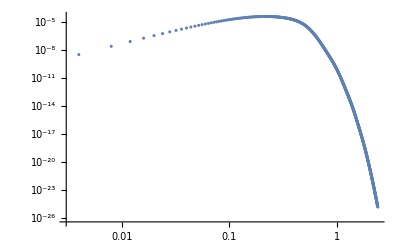

```mathematica
κ=1/4; (*surface gravity*)

For[l=1,l<=4,l++,
𝒩1[l]=Table[ (data1[l][[q,2]])/(Exp[(2 π ((data1[l][[q,1]])))/(κ)]-1),{q,1,Length[data1[l]]}]
]
S𝒩1=Sum[(2l+1)𝒩1[l],{l,1,4}];
Σ𝒩1=Table[{q (0.004),S𝒩1[[q]]},{q,1,Length[S𝒩1]}];
Plot1=ListLogLogPlot[Σ𝒩1]
```

### fitted GBF to spectrum (best-fit parameters obtained somewhere else)

```mathematica
a21=-0.790;b21=-2.770;c21=6.923;
a22= 1.0997; b22= 2.059; c22 = -5.146;
a23=0.957; b23= 2.065; c23= -4.853; d23= -0.138;
a24=0.928; b24=2.068;c24= -4.760;d24= -0.240;e24=-0.031;
Subscript[Γ, 1A][ω_, l_] := 0.5*(Erf[ a21 + b21*l+ c21*ω ]+1)
Subscript[Γ, 1B][ω_, l_]:= Erf[Erfc[a22+b22*l+c22*ω]]
Subscript[Γ, 1C][ω_, l_]:= Erf[Erfc[a23+b23*l+c23*ω+d23*ω^2]]
Subscript[Γ, 1D][ω_, l_]:= Erf[Erfc[a24+b24*l+c24*ω+d24*ω^2+e24*ω^3]]

Subscript[S, 1C][ω_]:= 2*Sum[ (2l+1)Subscript[Γ, 1C][ω, l]/(Exp[2 π ω/κ]-1),{l,1,4}];
(*Plot1=LogLogPlot[Subscript[S, 1C][ω],{ω,0,2.6}];
Plot2=LogLogPlot[Subscript[S, 1C][ω],{ω,0,2.6},PlotStyle->Red];
Show[Plot1,Plot2]*)
```

## Integrated Spectrum

```mathematica
Subscript[H, 0]= 72;
Subscript[Ω, m]=0.253;
Subscript[z, max]=500;
H[z_]:=Subscript[H, 0]*Sqrt[Subscript[Ω, m]*(1+z)^3+(1-Subscript[Ω, m])];
```

### Fitted GBF Integrated Spectrum

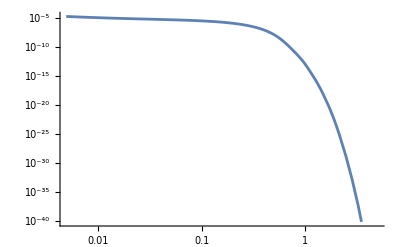

```mathematica
IntegratedS[w_]:=NIntegrate[H[z]^-1*Subscript[S, 1C][(1+z)*w],{z,0,500}]
LogLogPlot[IntegratedS[w],{w,0,5}]
```

### Fitted-truncated GBF spectrum

```mathematica
Res=0.5;

l=1;
T=Table[Abs[(Subscript[Γ, 1C][data1[l][[i,1]], l]-data1[l][[i,2]])]/data1[l][[i,2]],{i,1,Length[data1[l]]}];
For[i=1,i<=Length[data1[l]],i++,
If[T[[i]]>Res,imax=i]
];
Subscript[γ, 1C][ω_, 1]=HeavisideTheta[ω- data1[l][[imax,1]]]*Subscript[Γ, 1C][ω, 1];

l=2;
T=Table[Abs[(Subscript[Γ, 1C][data1[l][[i,1]], l]-data1[l][[i,2]])]/data1[l][[i,2]],{i,1,Length[data1[l]]}];
For[i=1,i<=Length[data1[l]],i++,
If[T[[i]]>Res,imax=i]
];
Subscript[γ, 1C][ω_, 2]=HeavisideTheta[ω- data1[l][[imax,1]]]*Subscript[Γ, 1C][ω, 2];

l=3;
T=Table[Abs[(Subscript[Γ, 1C][data1[l][[i,1]], l]-data1[l][[i,2]])]/data1[l][[i,2]],{i,1,Length[data1[l]]}];
For[i=1,i<=Length[data1[l]],i++,
If[T[[i]]>Res,imax=i]
];
Subscript[γ, 1C][ω_, 3]=HeavisideTheta[ω- data1[l][[imax,1]]]*Subscript[Γ, 1C][ω, 3];

l=4;
T=Table[Abs[(Subscript[Γ, 1C][data1[l][[i,1]], l]-data1[l][[i,2]])]/data1[l][[i,2]],{i,1,Length[data1[l]]}];
For[i=1,i<=Length[data1[l]],i++,
If[T[[i]]>Res,imax=i]
];
Subscript[γ, 1C][ω_, 4]=HeavisideTheta[ω- data1[l][[imax,1]]]*Subscript[Γ, 1C][ω, 4];

Subscript[ST, 1C][ω_]:=2*Sum[ (2l+1)Subscript[γ, 1C][ω, l]/(Exp[2 π ω/κ]-1),{l,1,4}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {159.172}. NIntegrate obtained 4.38856×10^-8 and 8.81101×10^-11 for the integral and error estimates.

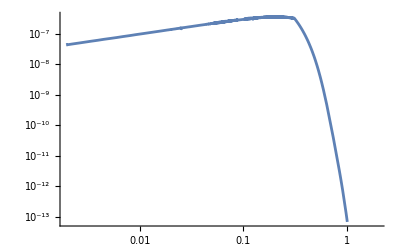

```mathematica
IntegratedST[w_]:=NIntegrate[H[z]^-1*Subscript[ST, 1C][(1+z)*w],{z,0,500}]
LogLogPlot[IntegratedST[w],{w,0,2}]
```